# 0D-U-I-SoC Model (α-Version)

```mathematica
SetOptions[Plot,Frame-> True,Axes-> True,PlotTheme-> "Detailed",AxesStyle->{Directive[Black,16],Black},LabelStyle-> {Directive[16]}];
SetOptions[ListPlot,Frame-> True,Axes-> True,PlotTheme-> "Detailed",AxesStyle->{Directive[Black,16],Black},LabelStyle-> {Directive[16]}];
SetOptions[RegionPlot,Frame-> True,Axes-> True,PlotTheme-> "Detailed",AxesStyle->{Directive[Black,16],Black},LabelStyle-> {Directive[16]}];
```

## Physical Constants

```mathematica
R=8.314;(*ideal gas constant [J/(K mol)]*)
F=96485;(*Faraday constant [C/mol]*)
f=F/(R T);(*inverse thermal voltage [V^-1]*)
fInv=(R T)/F;(*thermal voltage [V]*)
```

## Material Parameters

#### Molar Masses

```mathematica
molarMassSolvent=18.01528/1000;(*molar mass of pure water [kg/mol]*)
molarMassChloride=35.45/1000;(*molar mass of chloride [kg/mol]*)
molarMassTempo=214.353/1000;(*molar mass of TEMPTMA [kg/mol]*)
molarMassMethylViologen=186.26/1000;(* molar mass of methyl viologen (paraquat) [kg/mol]*)
molarMassOxNeg=molarMassMethylViologen+2*molarMassChloride;(*molar mass of methyl viologen dichloride [kg/mol]*)
molarMassRedNeg=molarMassMethylViologen+molarMassChloride;(*molar mass of methyl viologen chloride [kg/mol]*)
molarMassOxPos=molarMassTempo+2*molarMassChloride;(*molar mass of TEMPTMA dichloride [kg/mol]*)
molarMassRedPos=molarMassTempo+molarMassChloride;(*molar mass of TEMPTMA chloride [kg/mol]*)
```

#### Electrolyte Properties

```mathematica
Clear[TClMassDensFitFun,MVCl2MassDensFitFun,TCl2MassDensFitFun,MVClMassDensFitFun];
TClMassDensFitFun[c_]:=0.9970+0.03845*c;(*uncharged TEMPTMA*)
MVCl2MassDensFitFun[c_]:=0.9970+0.06832*c;(*uncharged methyl viologen*)
TCl2MassDensFitFun[c_]:=0.9968+0.05271*c;(*charged TEMPTMA*)
MVClMassDensFitFun[c_]:=0.9976+0.0594*c;(*charged methyl viologen*)
```

## Generic Mappings

### Number of moles and molar volumes to molar concentrations

```mathematica
cRedNeg[SOC_]:=nRedNeg[SOC]/(nSolventNeg[SOC]*molarVolSlvNeg[SOC]+nRedNeg[SOC]*molarVolRedNeg[SOC]+nOxNeg[SOC]*molarVolOxNeg[SOC]);
cOxNeg[SOC_]:=nOxNeg[SOC]/(nSolventNeg[SOC]*molarVolSlvNeg[SOC]+nRedNeg[SOC]*molarVolRedNeg[SOC]+nOxNeg[SOC]*molarVolOxNeg[SOC]);
cRedPos[SOC_]:=nRedPos[SOC]/(nSolventPos[SOC]*molarVolSlvPos[SOC]+nRedPos[SOC]*molarVolRedPos[SOC]+nOxPos[SOC]*molarVolOxPos[SOC]);
cOxPos[SOC_]:=nOxPos[SOC]/(nSolventPos[SOC]*molarVolSlvPos[SOC]+nRedPos[SOC]*molarVolRedPos[SOC]+nOxPos[SOC]*molarVolOxPos[SOC]);

molarConcSolventPosFun[cSolute_]:=(TClMassDensFitFun[cSolute]-cSolute*(molarMassRedPos))/molarMassSolvent;
molarConcSolventNegFun[cSolute_]:=(MVCl2MassDensFitFun[cSolute]-cSolute*(molarMassOxNeg))/molarMassSolvent;
On[Assert];
Assert[D[TClMassDensFitFun[cSolute],cSolute]== ((molarMassRedPos)+D[molarConcSolventPosFun[cSolute],cSolute]molarMassSolvent)]
Off[Assert];
```

### Number of moles to molalities

```mathematica
bRedNeg[SOC_]:=nRedNeg[SOC]/(nSolventNeg[SOC]*molarMassSolvent);(*molality of reduced species in negolyte [mol/kg]*)
bOxNeg[SOC_]:=nOxNeg[SOC]/(nSolventNeg[SOC]*molarMassSolvent);(*molality of oxidized species in negolyte [mol/kg]*)
bOxPos[SOC_]:=nOxPos[SOC]/(nSolventPos[SOC]*molarMassSolvent);(*molality of oxidized species in posolyte [mol/kg]*)
bRedPos[SOC_]:=nRedPos[SOC]/(nSolventPos[SOC]*molarMassSolvent);(*molality of reduced species in posolyte [mol/kg]*)
```

### Number of moles as a function of SOC in terms of the initial data

```mathematica
nRedNeg[SOC_]:=nRedSoc0Neg-(nOxNeg[SOC]-nOxSoc0Neg); (*[mol]*)
nOxNeg[SOC_]:=nOxSoc0Neg+SOC(nOxSoc1Neg-nOxSoc0Neg);(*[mol]*)
nOxPos[SOC_]:=nOxSoc0Pos-(nRedPos[SOC]-nRedSoc0Pos);(*[mol]*)
nRedPos[SOC_]:=nRedSoc0Pos+SOC(nRedSoc1Pos-nRedSoc0Pos);(*[mol]*)
nSolventNeg[SOC_]:=nSolventSoc0Neg+κd*(nRedPos[SOC]-nRedSoc0Pos);(*[mol]*)
nSolventPos[SOC_]:=nSolventSoc0Pos-κd*(nRedPos[SOC]-nRedSoc0Pos);(*[mol]*)
```

### Approximate Molar volumes

```mathematica
molarVolSlvNeg[SOC_]:=molarMassSolvent/MVCl2MassDensFitFun[0];(*approximate molar volume [L/mol] of solvent in negolyte*)
molarVolSlvPos[SOC_]:=molarMassSolvent/TClMassDensFitFun[0];(*approximate molar volume [L/mol] of solvent in posolyte*)
Clear[molarVolOxPos,molarVolRedPos, molarVolOxNeg, molarVolRedNeg];
molarVolPosSoc0=Solve[cRedPos[0]==cRedSoc0Pos&&molarVolRedPos[0]== molarVolOxPos[0],{molarVolRedPos[0], molarVolOxPos[0]}];
molarVolNegSoc0=Solve[cOxNeg[0]==cOxSoc0Neg&&molarVolRedNeg[0]== molarVolOxNeg[0],{molarVolRedNeg[0], molarVolOxNeg[0]}];

molarVolRedNeg[SOC_]=molarVolNegSoc0⟦1,1,2⟧;
molarVolOxNeg[SOC_]=molarVolNegSoc0⟦1,2,2⟧;
molarVolRedPos[SOC_]=molarVolPosSoc0⟦1,1,2⟧;
molarVolOxPos[SOC_]=molarVolPosSoc0⟦1,2,2⟧;
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

## Current to Voltage Transformations

```mathematica
eNeg0Formal[SOC_]:=eNeg0;
ePos0Formal[SOC_]:=ePos0;
eNernstNeg[SOC_]:=eNeg0Formal[SOC]-fInv Log[(bRedNeg[SOC])/(bOxNeg[SOC])];
eNernstPos[SOC_]:=ePos0Formal[SOC]-fInv Log[(bRedPos[SOC])/(bOxPos[SOC])];
totCurrentToCurrentDensityPos[totCurrent_]:=totCurrent/totElArea;
totCurrentToCurrentDensityNeg[totCurrent_]:=-totCurrent/totElArea;
ηBvNeg[SOC_,totCurrent_]:=ηBvNegImpl[SOC,totCurrentToCurrentDensityNeg[totCurrent]];
ηBvNegImpl[SOC_,currentDensity_]:=2 fInv Log[(currentDensity+Sqrt[currentDensity^2+4 gOxNeg[SOC,currentDensity]* gRedNeg[SOC,currentDensity]* exchangeCurrentNeg[SOC]^2])/(2 gRedNeg[SOC,currentDensity] *exchangeCurrentNeg[SOC])];
ηBvPos[SOC_,totCurrent_]:=ηBvPosImpl[SOC,totCurrentToCurrentDensityPos[totCurrent]];
ηBvPosImpl[SOC_,currentDensity_]:=2 fInv Log[(currentDensity+Sqrt[currentDensity^2+4 gOxPos[SOC,currentDensity]* gRedPos[SOC,currentDensity]*exchangeCurrentPos[SOC]^2])/(2 gRedPos[SOC,currentDensity]* exchangeCurrentPos[SOC])];

gOxNeg[SOC_,currentDensity_]:=(bOxNeg[SOC]-ΔbOxNeg[SOC,currentDensity])/bOxNeg[SOC];
gRedNeg[SOC_,currentDensity_]:=(bRedNeg[SOC]-ΔbRedNeg[SOC,currentDensity])/bRedNeg[SOC];
gOxPos[SOC_,currentDensity_]:=(bOxPos[SOC]-ΔbOxPos[SOC,currentDensity])/bOxPos[SOC];
gRedPos[SOC_,currentDensity_]:=(bRedPos[SOC]-ΔbRedPos[SOC,currentDensity])/bRedPos[SOC];
 exchangeCurrentNeg[SOC_]:=F kneg *10^3* Sqrt[bRedNeg[SOC]*bOxNeg[SOC]];
 exchangeCurrentPos[SOC_]:=F kpos *10^3*Sqrt[bRedPos[SOC]*bOxPos[SOC]];

ηBvActNeg[SOC_,totCurrent_]:=2*fInv *ArcSinh[(-totCurrentToCurrentDensityNeg[totCurrent])/(2* exchangeCurrentNeg[SOC])];
ηBvActPos[SOC_,totCurrent_]:=2*fInv *ArcSinh[totCurrentToCurrentDensityPos[totCurrent]/(2* exchangeCurrentPos[SOC])];

ηBvConcNeg[SOC_,totCurrent_]:=Piecewise[{{-2 fInv Log[gOxNeg[SOC,-totCurrentToCurrentDensityNeg[totCurrent]]],totCurrent≤ 0}},-2 fInv Log[gRedNeg[SOC,-totCurrentToCurrentDensityNeg[totCurrent]]]];
ηBvConcPos[SOC_,totCurrent_]:=Piecewise[{{2 fInv Log[gOxPos[SOC,totCurrentToCurrentDensityPos[totCurrent]]],totCurrent≤ 0}},-2 fInv Log[gRedPos[SOC,totCurrentToCurrentDensityPos[totCurrent]]]];

ρSolventKgPerQubicMeter=10^3;
ΔbOxNeg[SOC_ ,currentDensity_]:=-currentDensity/(km  F)*1/ρSolventKgPerQubicMeter;
ΔbRedNeg[SOC_ ,currentDensity_]:=currentDensity/(km F)*1/ρSolventKgPerQubicMeter;
ΔbOxPos[SOC_,currentDensity_]:=-currentDensity/(km F)*1/ρSolventKgPerQubicMeter;
ΔbRedPos[SOC_,currentDensity_]:=currentDensity/(km F)*1/ρSolventKgPerQubicMeter;
```

```mathematica
limitingCurrentDensityPos[SOC_,currentDensity_]:=If[currentDensity≥ 0,(km*ρSolventKgPerQubicMeter*F)*bRedPos[SOC],-(km*ρSolventKgPerQubicMeter*F)*bOxPos[SOC]];
limitingCurrentDensityNeg[SOC_,currentDensity_]:=If[currentDensity≥ 0,(km*ρSolventKgPerQubicMeter*F)*bOxNeg[SOC],-(km*ρSolventKgPerQubicMeter*F)*bRedNeg[SOC]];
limitingCurrentDensity[SOC_,currentDensity_]:=If[currentDensity≥ 0,Min[limitingCurrentDensityPos[SOC,currentDensity],limitingCurrentDensityNeg[SOC,currentDensity]],Max[limitingCurrentDensityPos[SOC,currentDensity],limitingCurrentDensityNeg[SOC,currentDensity]]];
limitingTotCurrent[SOC_,currentDensity_]:=limitingCurrentDensity[SOC,currentDensity]*totElArea;
```

```mathematica
ηBvAct[SOC_,totCurrent_]:=ηBvActPos[SOC,totCurrent]-ηBvActNeg[SOC,totCurrent];
ηBvConc[SOC_,totCurrent_]:=ηBvConcPos[SOC,totCurrent] -ηBvConcNeg[SOC,totCurrent];
ηBv[SOC_,totCurrent_]:=ηBvPos[SOC,totCurrent] -ηBvNeg[SOC,totCurrent];
ηElRes[SOC_,totCurrent_]:=totCurrent*rCell;
ηTot[SOC_,totCurrent_]:=ηBvAct[SOC,totCurrent]+ηElRes[SOC,totCurrent];
```

```mathematica
cellVoltageOcv[SOC_]:=(eNernstPos[SOC]-eNernstNeg[SOC]);
cellVoltageOcvAndBv[SOC_,totCurrent_]:=cellVoltageOcv[SOC]+ηBv[SOC,totCurrent];
cellVoltageOcvAndBvAndOhmic[SOC_,totCurrent_]:=cellVoltageOcv[SOC]+ηBv[SOC,totCurrent]+ ηElRes[SOC,totCurrent];
```

```mathematica
convertTotCurrentAmpToCurrentDensityAmpPerCm2[totCurrent_,memArea_]:=totCurrent*1000/(memArea*100^2);
```

### Specification of Experimental Parameters and Conditions

#### Set Cell and Operating Parameters

```mathematica
nSolventSoc0Neg=molarConcSolventNegFun[cOxSoc0Neg]*electrolyteVol;
nSolventSoc0Pos=molarConcSolventPosFun[cRedSoc0Pos]*electrolyteVol;
nOxSoc1Neg=nOxSoc0Neg-Min[nOxSoc0Neg,nRedSoc0Pos];
nRedSoc1Pos=nRedSoc0Pos-Min[nOxSoc0Neg,nRedSoc0Pos];
```

```mathematica
T=298.15;(*constant temperature [K]*)
electrolyteVol=1/100;(*initial electrolyte volume per compartment [L]*)
cOxSoc0Neg=1.49;(*molar concentration [mol/L]*)
cRedSoc0Pos=1.12;(*molar concentration [mol/L]*)
nRedSoc0Neg=0;(*initial amount of reduced species in negolyte (for a fully discharged battery) [mol]*)
nOxSoc0Pos=0;(*initial amount of oxidized species in posolyte (for a fully discharged battery) [mol]*)
nOxSoc0Neg=cOxSoc0Neg*electrolyteVol;(*initial amount of oxidized species in negolyte (for a fully discharged battery) [mol]*)
nRedSoc0Pos=cRedSoc0Pos*electrolyteVol;(*initial amount of reduced species in posolyte (for a fully discharged battery) [mol]*)
elLength=0.4/100;(*length in through-plance direction of the MEA [m]*)
elWidth=2.236/100;(*witdth of the electrode compartment [m]*)
elHeight=2.236/100;(*height of the electrode compartment [m]*)
specElArea=2*10^5;(*specific surface area of electrode [m^-1]*)
flowRateMLperMin=16;(*volumetric flow rate [mL/min]*)
u=(flowRateMLperMin/(1000*1000))/(60*(elWidth*elLength));(*superficial velocity of electrolyte [m/s]*)
rCell=0.286;(*Electrical cell resistance [V/A]*)
eNeg0=-0.63;(*standard half-cell potential of Methyl-Viologen [V]*)
ePos0=0.62;(*standard half-cell potential of TEMPTMA [V]*)
elCurrentDensity=-80/1000*(100)^2;(*Current density [A/m^2]*)
kneg=3.3*10^-5;(*3.6*10^-8;*)(*reaction constant at negative electrode [m/s]*)
kpos=4.2*10^-5;(*6.5*10^-8;*)(*reaction constant at positive electrode [m/s]*)
aParam=4*10^-5;(*mass transport limitation factor [(m/s)^0.9]*)
bParam=0.9;(*mass transport limitation factor [-]*)
κd=6;(*electro-osmotic drag coefficient [-]*)

elVol=elLength*elWidth*elHeight;(*total electrode volume [m^3]*)
memArea=elWidth*elHeight;(*membrane area [m^2]*)
totElCurrent=elCurrentDensity * memArea;(*total discharge electric current [A]*)
absTotElCurrent=Abs[totElCurrent];(*absolute value of total current [A]*)
totElArea=specElArea*elVol;(*total electrode area [m^2]*)
km=aParam*u^bParam;(*mass transfer coefficient [m/s]*)
```

### SOC and El. Current Limits

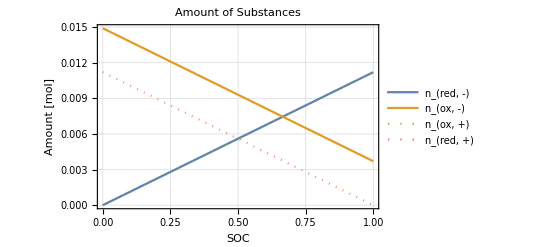

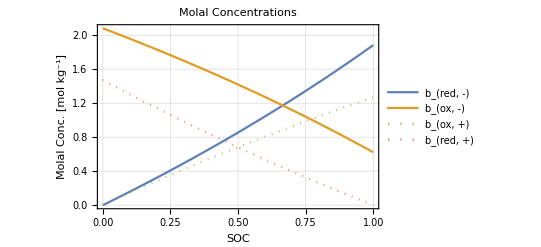

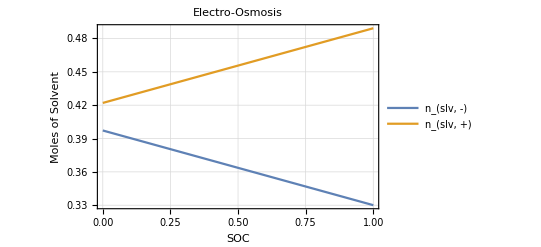

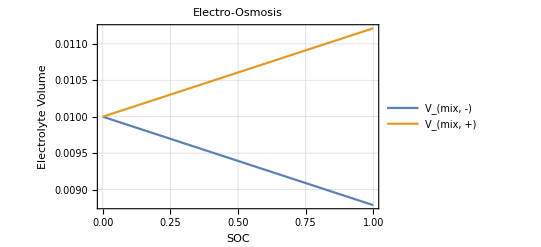

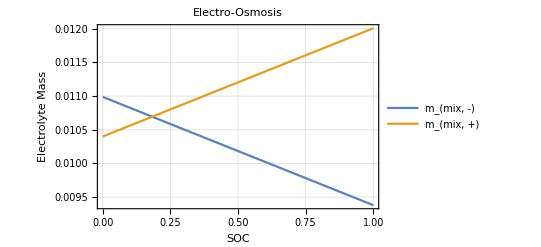

```mathematica
pAmountOfSubstanceVsSoc=Plot[{nRedNeg[SOC],nOxNeg[SOC],nOxPos[SOC],nRedPos[SOC]},{SOC,0,1},FrameLabel-> {"SOC","Amount [mol]"},PlotLabel-> "Amount of Substances",PlotLegends->Placed[{"n_(red, -)","n_(ox, -)","n_(ox, +)","n_(red, +)"},Below],PlotStyle->{Full,Full,Dotted,Dotted}]
pMolalConcentrationsVsSoc=Plot[{bRedNeg[SOC],bOxNeg[SOC],bOxPos[SOC],bRedPos[SOC]},{SOC,0,1},FrameLabel-> {"SOC","Molal Conc. [mol kg^-1]"},PlotLabel-> "Molal Concentrations",PlotLegends->Placed[{"b_(red, -)","b_(ox, -)","b_(ox, +)","b_(red, +)"},Below],PlotStyle->{Full,Full,Dotted,Dotted}]
pMolesOfSolventVsSoc=Plot[{nSolventNeg[SOC],nSolventPos[SOC]},{SOC,0,1},FrameLabel-> {"SOC","Moles of Solvent"},PlotLabel-> "Electro-Osmosis",PlotLegends->Placed[{"n_(slv, -)","n_(slv, +)"},Below],PlotStyle->{Full,Full,Dotted,Dotted}]
volElectrolyteNeg[SOC_]:=nSolventNeg[SOC]*molarVolSlvNeg[SOC]+nRedNeg[SOC]*molarVolRedNeg[SOC]+nOxNeg[SOC]*molarVolOxNeg[SOC];
volElectrolytePos[SOC_]:=nSolventPos[SOC]*molarVolSlvPos[SOC]+nRedPos[SOC]*molarVolRedPos[SOC]+nOxPos[SOC]*molarVolOxPos[SOC];
massElectrolyteNeg[SOC_]:=nSolventNeg[SOC]*molarMassSolvent+nRedNeg[SOC]*molarMassRedNeg+nOxNeg[SOC]*molarMassOxNeg;
massElectrolytePos[SOC_]:=nSolventPos[SOC]*molarMassSolvent+nRedPos[SOC]*molarMassRedPos+nOxPos[SOC]*molarMassOxPos;
pElectrolyteVolVsSoc=Plot[{volElectrolyteNeg[SOC],volElectrolytePos[SOC]},{SOC,0,1},FrameLabel-> {"SOC","Electrolyte Volume"},PlotLabel-> "Electro-Osmosis",PlotLegends->Placed[{"V_(mix, -)","V_(mix, +)"},Below],PlotStyle->{Full,Full,Dotted,Dotted}]
pElectrolyteMassVsSoc=Plot[{massElectrolyteNeg[SOC],massElectrolytePos[SOC]},{SOC,0,1},FrameLabel-> {"SOC","Electrolyte Mass"},PlotLabel-> "Electro-Osmosis",PlotLegends->Placed[{"m_(mix, -)","m_(mix, +)"},Below],PlotStyle->{Full,Full,Dotted,Dotted}]
```

### Voltage Vs SOC Plots

```mathematica
socChargingLimit=NSolve[N[limitingTotCurrent[SOC,1.0]]==absTotElCurrent,SOC]⟦1,1,2⟧;
socDischargingLimit=NSolve[N[limitingTotCurrent[SOC,-1.0]]==-absTotElCurrent,SOC]⟦1,1,2⟧;
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

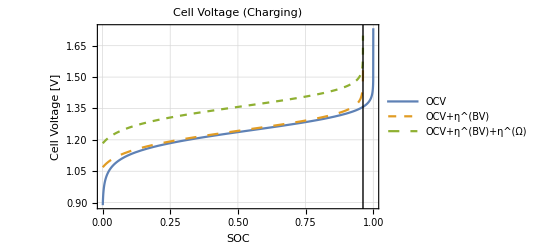

```mathematica
pVoltageVsSocWhenCharging=Plot[{
cellVoltageOcv[soc],
cellVoltageOcvAndBv[soc,absTotElCurrent],
cellVoltageOcvAndBvAndOhmic[soc,absTotElCurrent]
},{soc,0.001,1},
PlotLegends->{"OCV","OCV+η^(BV)","OCV+η^(BV)+η^(Ω)"},PlotLabel-> "Cell Voltage (Charging)",FrameLabel->{"SOC","Cell Voltage [V]"},Epilog-> {Style[Line[{{socChargingLimit,-10},{socChargingLimit,10}}],Dashed]},
PlotStyle-> {Full,Dashing[{0.02,0.02}],Dashed,DotDashed,Dotted}]
```

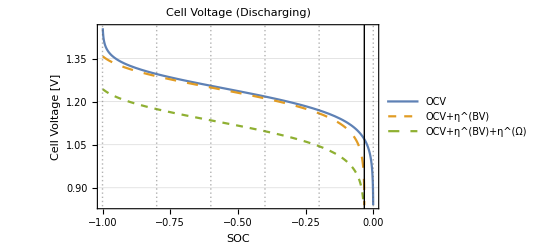

```mathematica
pVoltageVsSocWhenDischarging=Plot[{
cellVoltageOcv[soc],
cellVoltageOcvAndBv[soc,-absTotElCurrent],
cellVoltageOcvAndBvAndOhmic[soc,-absTotElCurrent]
},{soc,0,0.999},
PlotLegends->{"OCV","OCV+η^(BV)","OCV+η^(BV)+η^(Ω)"},
PlotStyle-> {Full,Dashing[{0.02,0.02}],Dashed,DotDashed,Dotted},
PlotLabel-> "Cell Voltage (Discharging)",ScalingFunctions->{"Reverse"},FrameLabel->{"SOC","Cell Voltage [V]"},Epilog-> {Style[Line[{{-socDischargingLimit,-10},{-socDischargingLimit,10}}],Dashed]}]
```

### Polarization Plots

```mathematica
δ=10^-3;
socDataPointSpacing=0.01;
PolarizationPlotSOC=0.99;
elDensityDischargeRoot=FindMinimum[cellVoltageOcvAndBvAndOhmic[PolarizationPlotSOC,iCurrentDensityMVperCM2*(memArea*100^2)/10^3]^2,iCurrentDensityMVperCM2]⟦2,1,2⟧;
elDensityDischargeLim=Max[Max[limitingCurrentDensity[PolarizationPlotSOC,-1.0]/((memArea*100^2)/10^3),elDensityDischargeRoot],-600];
maxCellVoltageSol=cellVoltageOcvAndBvAndOhmic[PolarizationPlotSOC,0];
currentDataPointSpacing=Abs[elDensityDischargeLim]/100;
```

```mathematica
currentAndSocToVoltageTable=Table[{iCurrentDensityMVperCM2,soc,If[iCurrentDensityMVperCM2 (memArea*100^2)/10^3 ≥limitingTotCurrent[soc,-1.0]+δ,cellVoltageOcvAndBvAndOhmic[soc,iCurrentDensityMVperCM2 (memArea*100^2)/10^3],0]},{soc,0.001,0.999,socDataPointSpacing},{iCurrentDensityMVperCM2,elDensityDischargeLim,0,currentDataPointSpacing}];
currentAndSocToVoltageTable=Flatten[currentAndSocToVoltageTable,1];
currentAndSocToPowerDensityTable=Table[{currentAndSocToVoltageTable⟦i,1⟧,currentAndSocToVoltageTable⟦i,2⟧,currentAndSocToVoltageTable⟦i,3⟧*Abs[currentAndSocToVoltageTable⟦i,1⟧]},{i,1,Length[currentAndSocToVoltageTable]}];
```

```mathematica
socAtDischargeLim=FindMinimum[{(elDensityDischargeLim  (memArea*100^2)/10^3- limitingTotCurrent[soc,-1.0])^2,soc≥ 0&&soc≤ 1},{soc}]⟦2,1,2⟧;
```

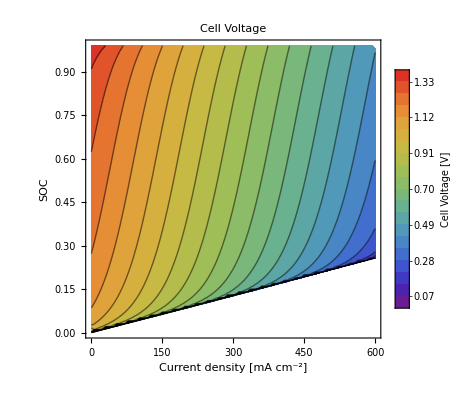

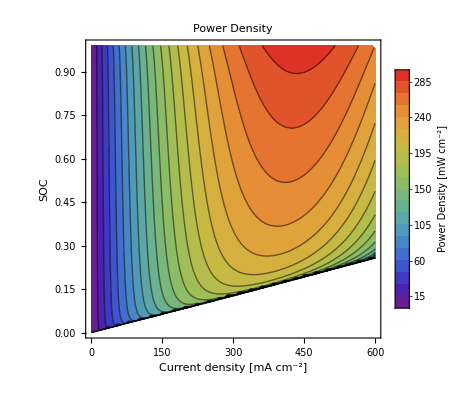

```mathematica
maxCellVoltageSol=Ceiling[Max[Table[currentAndSocToVoltageTable⟦i,3⟧,{i,1,Length[currentAndSocToVoltageTable]}]],0.1];
pCellVoltageVsCurrentDensityAndSoc=ListContourPlot[currentAndSocToVoltageTable,
RegionFunction->Function[{elDensityDischargeLim,soc},-elDensityDischargeLim  (memArea*100^2)/10^3≥ limitingTotCurrent[soc,-1.0]],PlotRangePadding->None,
FrameLabel-> {"Current density [mA cm^-2]","SOC"},
PlotLabel-> "Cell Voltage",PlotRange->All,Contours->Table[i,{i,0,maxCellVoltageSol,maxCellVoltageSol/20}],ColorFunction->(ColorData["Rainbow"][Rescale[#,{0,maxCellVoltageSol}]]&),ColorFunctionScaling->False,PlotLegends->Placed[BarLegend[Automatic,LegendLabel-> "Cell Voltage [V]"],Right],ScalingFunctions->{"Reverse",None},Epilog->{Style[Line[{{0,0},{600,socAtDischargeLim}}],Thickness[0.01]]},LabelStyle->Directive[18]]

maxCellPowerDensitySol=Ceiling[Max[Table[currentAndSocToPowerDensityTable⟦i,3⟧,{i,1,Length[currentAndSocToPowerDensityTable]}]],10];
pCellPowerDensityVsCurrentDensityAndSoc=ListContourPlot[currentAndSocToPowerDensityTable,
RegionFunction->Function[{elDensityDischargeLim,soc},-elDensityDischargeLim  (memArea*100^2)/10^3≥limitingTotCurrent[soc,-1.0]],PlotRangePadding->None,
FrameLabel-> {"Current density [mA cm^-2]","SOC"},
PlotLabel-> "Power Density",PlotRange->All,Contours->Table[i,{i,0,maxCellPowerDensitySol,maxCellPowerDensitySol/20}],ColorFunction->(ColorData["Rainbow"][Rescale[#,{0,maxCellPowerDensitySol}]]&),ColorFunctionScaling->False,PlotLegends->Placed[BarLegend[Automatic,LegendLabel-> "Power Density [mW cm^-2]"],Right],ScalingFunctions->{"Reverse",None},Epilog->{Style[Line[{{0,0},{600,socAtDischargeLim}}],Thickness[0.01]]},LabelStyle->Directive[18]]
```